{{u→Function[{t},-1/(1+4 π^4)2 ⅇ^-t (-2 π Cos[t]+2 ⅇ^t π Cos[t]^2 Cos[2 π t]-4 π^3 Sin[t]+2 ⅇ^t π Cos[2 π t] Sin[t]^2-ⅇ^t Cos[t]^2 Sin[2 π t]+2 ⅇ^t π^2 Cos[t]^2 Sin[2 π t]-ⅇ^t Sin[t]^2 Sin[2 π t]+2 ⅇ^t π^2 Sin[t]^2 Sin[2 π t])]}}

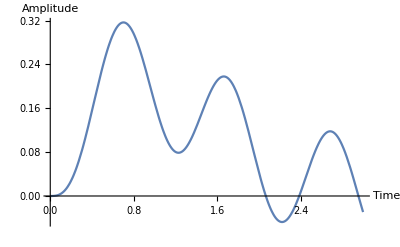

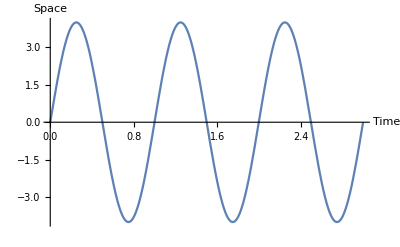

{t,u,f}

C:\Users\Razer\OneDrive - Technische Universität Graz\Dokumente\Uni\6.Semester\BAC\Code_bac\PI_GP_regressor\data_files\damped_m1k2b1.csv

```mathematica
(*This notebook computes the analytical solution for a damped oscillator. There are several different examples with different forcing terms*)(**)
L=1;
(*forcing term*)
f[t_]:= Sin[2*Pi*t]*4; 
(*lets define all the parameters*)
m=1;
gamma=2;
k=2;
tm = 3; (*lenth of the time-domain*)
(*now we define the differential equation*)
eqn=m*D[u[t],{t,2}]+gamma*D[u[t],{t,1}]+k*u[t]==f[t];

initialConditions={u[0]==0,Derivative[1][u][0]==0};

sol=DSolve[{eqn,initialConditions},u,t]

Plot[Evaluate[u[t]/. sol],{t,0,tm},AxesLabel->{"Time","Amplitude"}]
Plot[Evaluate[f[t]], {t,0,tm},AxesLabel->{"Time","Space","Amplitude"}]
soln=u[t]/. First@sol;
data=Table[{tval,soln/. t->tval,f[tval]},{tval,0,tm,0.01}];
header = {"t","u","f"}
filename="C:\\Users\\Razer\\OneDrive - Technische Universität Graz\\Dokumente\\Uni\\6.Semester\\BAC\\Code_bac\\PI_GP_regressor\\data_files\\damped_m1k2b1.csv";
If[FileExistsQ[filename],DeleteFile[filename]];
CreateFile[filename];
dataWithHeader=Prepend[data,header];
(*now we export the data*)
Export[filename, dataWithHeader]
```

{{u→InterpolatingFunction[…]}}

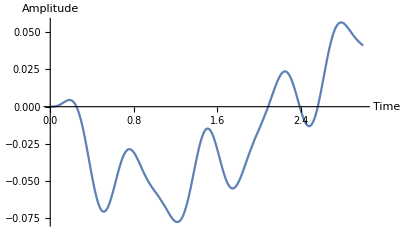

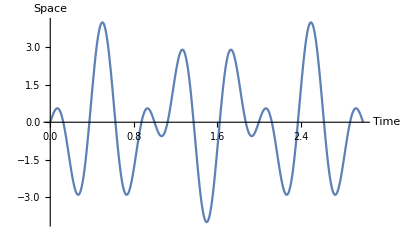

{t,u,f}

C:\Users\Razer\OneDrive - Technische Universität Graz\Dokumente\Uni\6.Semester\BAC\Code_bac\PI_GP_regressor\data_files\damped_second.csv

```mathematica
L=1;
f[t_]:= Sin[Pi*t]*4*Cos[4*Pi*t];
m=1;
gamma=0.2;
k=2;
tm = 3;
eqn=m*D[u[t],{t,2}]+gamma*D[u[t],{t,1}]+k*u[t]==f[t];

initialConditions={u[0]==0,Derivative[1][u][0]==0};

sol=NDSolve[{eqn,initialConditions},u,{t,0,tm}]

Plot[Evaluate[u[t]/. sol],{t,0,tm},AxesLabel->{"Time","Amplitude"}]
Plot[Evaluate[f[t]], {t,0,tm},AxesLabel->{"Time","Space","Amplitude"}]
soln=u[t]/. First@sol;(*This applies the rules from sol to u[t]*)
data=Table[{tval,Re[soln/. t->tval],f[tval]},{tval,0,tm,0.01}];(*This replaces each t in soln and f with the actual values*)
header = {"t","u","f"}
filename="C:\\Users\\Razer\\OneDrive - Technische Universität Graz\\Dokumente\\Uni\\6.Semester\\BAC\\Code_bac\\PI_GP_regressor\\data_files\\damped_second.csv";
If[FileExistsQ[filename],DeleteFile[filename]];
CreateFile[filename];
dataWithHeader=Prepend[data,header];
Export[filename, dataWithHeader]
```

{{u→InterpolatingFunction[…]}}

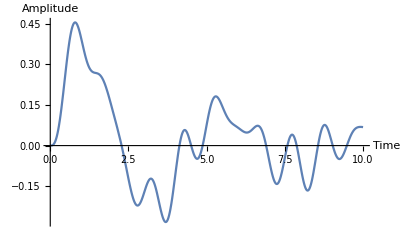

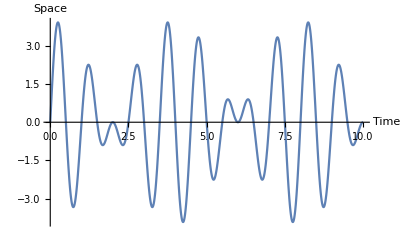

{t,u,f}

C:\Users\Razer\OneDrive - Technische Universität Graz\Dokumente\Uni\6.Semester\BAC\Code_bac\PI_GP_regressor\data_files\damped_third.csv

```mathematica
L=1;
f[t_]:= Sin[2*Pi*t]*4*Cos[Pi/4*t];
m=1;
gamma=0.5;
k=2;
tm = 10;
eqn=m*D[u[t],{t,2}]+gamma*D[u[t],{t,1}]+k*u[t]==f[t];

initialConditions={u[0]==0,Derivative[1][u][0]==0};

sol=NDSolve[{eqn,initialConditions},u,{t,0,tm}]

Plot[Evaluate[u[t]/. sol],{t,0,tm},AxesLabel->{"Time","Amplitude"}]
Plot[Evaluate[f[t]], {t,0,tm},AxesLabel->{"Time","Space","Amplitude"}]
soln=u[t]/. First@sol;(*This applies the rules from sol to u[t]*)
data=Table[{tval,soln/. t->tval,f[tval]},{tval,0,tm,0.01}];(*This replaces each t in soln and f with the actual values*)
header = {"t","u","f"}
filename="C:\\Users\\Razer\\OneDrive - Technische Universität Graz\\Dokumente\\Uni\\6.Semester\\BAC\\Code_bac\\PI_GP_regressor\\data_files\\damped_third.csv";
If[FileExistsQ[filename],DeleteFile[filename]];
CreateFile[filename];
dataWithHeader=Prepend[data,header];
Export[filename, dataWithHeader]
```